```mathematica
SetDirectory[NotebookDirectory[]]
```

D:\Administrator\ProgramFile\Mathematica

#### X(3872)

```mathematica
data=Import["X_3872_all.dat"];
```

```mathematica
(*define a function for Lorentz boost from the lab frame to DD* rest frame*)

flab[px_,py_,pz_,kx_,ky_,kz_]:=Module[{p,k,t},p={px,py,pz};k={kx,ky,kz};t=Sum[(p[[i]]-k[[i]])^2,{i,1,3}];Sqrt[t]]
```

```mathematica
fLB[Ep_,px_,py_,pz_,Ek_,kx_,ky_,kz_]:=Module[{β,γ,q,Etot,qvec,kvec,costheta,k,kper,kpar,kparstar,Ekk,kstar},q=Sqrt[(px+kx)^2+(py+ky)^2+(pz+kz)^2];Etot=Ep+Ek;β=q/Etot;γ=1/Sqrt[1-β^2];qvec={px+kx,py+ky,pz+kz};kvec={px-kx,py-ky,pz-kz};
Ekk=Ep-Ek;
k=Sqrt[Sum[kvec[[i]]^2,{i,1,3}]];costheta=Sum[qvec[[i]]*kvec[[i]],{i,1,3}]/(k*q);kper=k*Sqrt[1-costheta^2];kpar=k*costheta;kparstar=-γ*β*Ekk+γ*kpar;kstar=Sqrt[kparstar^2+kper^2]]
```

```mathematica
KdistributionLB=Table[fLB[data[[i]][[14]],data[[i]][[11]],data[[i]][[12]],data[[i]][[13]],data[[i+2]][[14]],data[[i+2]][[11]],data[[i+2]][[12]],data[[i+2]][[13]]],{i,1,119879,4}];
```

```mathematica
kk=Table[{i,fLB[data[[i]][[14]],data[[i]][[11]],data[[i]][[12]],data[[i]][[13]],data[[i+2]][[14]],data[[i+2]][[11]],data[[i+2]][[12]],data[[i+2]][[13]]]},{i,1,119879,4}];
kb=Table[{i,flab[data[[i]][[11]],data[[i]][[12]],data[[i]][[13]],data[[i+2]][[11]],data[[i+2]][[12]],data[[i+2]][[13]]]},{i,1,119879,4}];
```

```mathematica
tcomp=Table[kk[[i,2]]-kb[[i,2]],{i,1,29970}];
```

```mathematica
(*Pan: Please check whether you obtin the same result. kk and kb are the lists of the relative momentum after and before Lorent Boost*)
```

```mathematica
Min[kk]
Min[kb]
```

0.189332

0.190384

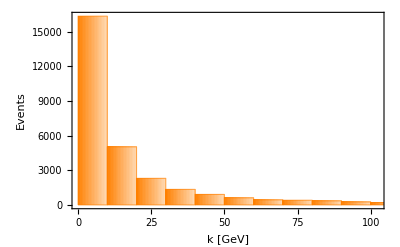

```mathematica
Histogram[KdistributionLB,{10},ChartElementFunction->"FadingRectangle",ChartStyle->Orange,Frame->True,FrameLabel->{"k [GeV]","Events"},LabelStyle->Directive[Black,Thickness[20],20,FontFamily->"Times"]]
```

```mathematica
Min[KdistributionLB]
```

0.189332

```mathematica
(*select events for k<mpi*)
```

```mathematica
Fselectevent[list_,limit_]:=Module[{ll,tt},ll=Length[list];tt={};Do[If[list[[i]]<limit,AppendTo[tt,list[[i]]]],{i,1,ll}];tt]
```

```mathematica
mpi=0.140;
```

```mathematica
t0=Fselectevent[KdistributionLB,mpi/2];
t1=Fselectevent[KdistributionLB,mpi];
t2=Fselectevent[KdistributionLB,2*mpi];
```

```mathematica
t3=Fselectevent[KdistributionLB,2*mpi*10];
t4=Fselectevent[KdistributionLB,2*mpi*100];
```

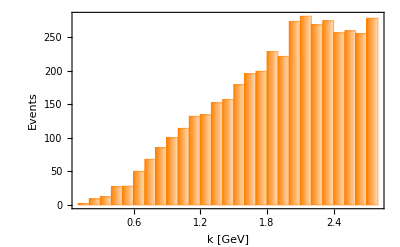

```mathematica
Histogram[t3,{0.1},ChartElementFunction->"FadingRectangle",ChartStyle->Orange,Frame->True,FrameLabel->{"k [GeV]","Events"},LabelStyle->Directive[Black,Thickness[20],20,FontFamily->"Times"]]
```

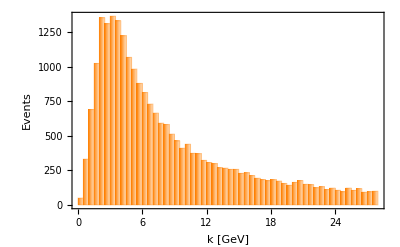

```mathematica
Histogram[t4,{0.5},ChartElementFunction->"FadingRectangle",ChartStyle->Orange,Frame->True,FrameLabel->{"k [GeV]","Events"},LabelStyle->Directive[Black,Thickness[20],20,FontFamily->"Times"]]
```

```mathematica
psi[r_]:=1/(Sqrt[2*Pi*a]*r)*Exp[-r/a]
```

```mathematica
Integrate[psi[r]^2*r^2*4*Pi,{r,0,Infinity}]
```

ConditionalExpression[1,Re[a]>0]

```mathematica
ConditionalExpression[1,Re[a]>0]
```

ConditionalExpression[1,Re[a]>0]

```mathematica
Integrate[psi[r]^2*r^4*4*Pi,{r,0,Infinity}]
```

ConditionalExpression[a^2/2,Re[a]>0]

```mathematica
ConditionalExpression[a^2/2,Re[a]>0]
```

ConditionalExpression[a^2/2,Re[a]>0]

#### Dbar Sigmac

```mathematica
data=Import["D_barSigma_c.dat"];
```

```mathematica
flab[px_,py_,pz_,kx_,ky_,kz_]:=Module[{p,k,t},p={px,py,pz};k={kx,ky,kz};t=Sum[(p[[i]]-k[[i]])^2,{i,1,3}];Sqrt[t]]
```

```mathematica
fLB[Ep_,px_,py_,pz_,Ek_,kx_,ky_,kz_]:=Module[{β,γ,q,Etot,qvec,kvec,costheta,k,kper,kpar,kparstar,Ekk,kstar},q=Sqrt[(px+kx)^2+(py+ky)^2+(pz+kz)^2];Etot=Ep+Ek;β=q/Etot;γ=1/Sqrt[1-β^2];qvec={px+kx,py+ky,pz+kz};kvec={px-kx,py-ky,pz-kz};
Ekk=Ep-Ek;
k=Sqrt[Sum[kvec[[i]]^2,{i,1,3}]];costheta=Sum[qvec[[i]]*kvec[[i]],{i,1,3}]/(k*q);kper=k*Sqrt[1-costheta^2];kpar=k*costheta;kparstar=-γ*β*Ekk+γ*kpar;kstar=Sqrt[kparstar^2+kper^2]]
```

```mathematica
KdistributionLB=Table[fLB[data[[i]][[14]],data[[i]][[11]],data[[i]][[12]],data[[i]][[13]],data[[i+2]][[14]],data[[i+2]][[11]],data[[i+2]][[12]],data[[i+2]][[13]]],{i,1,106771,4}];
```

```mathematica
kk=Table[{i,fLB[data[[i]][[14]],data[[i]][[11]],data[[i]][[12]],data[[i]][[13]],data[[i+2]][[14]],data[[i+2]][[11]],data[[i+2]][[12]],data[[i+2]][[13]]]},{i,1,106771,4}];
kb=Table[{i,flab[data[[i]][[11]],data[[i]][[12]],data[[i]][[13]],data[[i+2]][[11]],data[[i+2]][[12]],data[[i+2]][[13]]]},{i,1,106771,4}];
```

```mathematica
tcomp=Table[kk[[i,2]]-kb[[i,2]],{i,1,26643}];
```

```mathematica
(*Pan: Please check whether you obtin the same result. kk and kb are the lists of the relative momentum after and before Lorent Boost*)
```

```mathematica
Min[kk]
Min[kb]
```

0.106798

0.289095

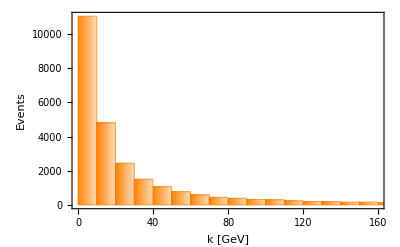

```mathematica
Histogram[KdistributionLB,{10},ChartElementFunction->"FadingRectangle",ChartStyle->Orange,Frame->True,FrameLabel->{"k [GeV]","Events"},LabelStyle->Directive[Black,Thickness[20],20,FontFamily->"Times"]]
```

```mathematica
Min[KdistributionLB]
```

0.106798

```mathematica
(*select events for k<mpi*)
```

```mathematica
Fselectevent[list_,limit_]:=Module[{ll,tt},ll=Length[list];tt={};Do[If[list[[i]]<limit,AppendTo[tt,list[[i]]]],{i,1,ll}];tt]
```

```mathematica
mpi=0.140;
```

```mathematica
t0=Fselectevent[KdistributionLB,mpi/2];
t1=Fselectevent[KdistributionLB,mpi];
t2=Fselectevent[KdistributionLB,2*mpi];
```

```mathematica
(*After the section, there is no event*)
```

```mathematica
t3=Fselectevent[KdistributionLB,2*mpi*10];
t4=Fselectevent[KdistributionLB,2*mpi*100];
```

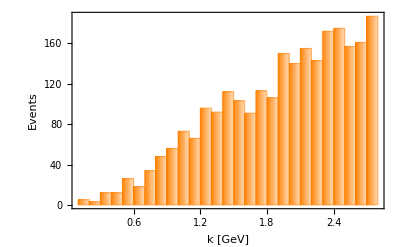

```mathematica
Histogram[t3,{0.1},ChartElementFunction->"FadingRectangle",ChartStyle->Orange,Frame->True,FrameLabel->{"k [GeV]","Events"},LabelStyle->Directive[Black,Thickness[20],20,FontFamily->"Times"]]
```

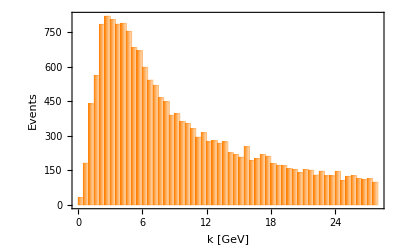

```mathematica
Histogram[t4,{0.5},ChartElementFunction->"FadingRectangle",ChartStyle->Orange,Frame->True,FrameLabel->{"k [GeV]","Events"},LabelStyle->Directive[Black,Thickness[20],20,FontFamily->"Times"]]
```

```mathematica
psi[r_]:=1/(Sqrt[2*Pi*a]*r)*Exp[-r/a]
```

```mathematica
Integrate[psi[r]^2*r^2*4*Pi,{r,0,Infinity}]
```

ConditionalExpression[1,Re[a]>0]

```mathematica
Integrate[psi[r]^2*r^4*4*Pi,{r,0,Infinity}]
```

ConditionalExpression[a^2/2,Re[a]>0]

#### Dbar Sigmastarc

```mathematica
data=Import["D_barSigma_star_c.dat"];
```

```mathematica
flab[px_,py_,pz_,kx_,ky_,kz_]:=Module[{p,k,t},p={px,py,pz};k={kx,ky,kz};t=Sum[(p[[i]]-k[[i]])^2,{i,1,3}];Sqrt[t]]
```

```mathematica
fLB[Ep_,px_,py_,pz_,Ek_,kx_,ky_,kz_]:=Module[{β,γ,q,Etot,qvec,kvec,costheta,k,kper,kpar,kparstar,Ekk,kstar},q=Sqrt[(px+kx)^2+(py+ky)^2+(pz+kz)^2];Etot=Ep+Ek;β=q/Etot;γ=1/Sqrt[1-β^2];qvec={px+kx,py+ky,pz+kz};kvec={px-kx,py-ky,pz-kz};
Ekk=Ep-Ek;
k=Sqrt[Sum[kvec[[i]]^2,{i,1,3}]];costheta=Sum[qvec[[i]]*kvec[[i]],{i,1,3}]/(k*q);kper=k*Sqrt[1-costheta^2];kpar=k*costheta;kparstar=-γ*β*Ekk+γ*kpar;kstar=Sqrt[kparstar^2+kper^2]]
```

```mathematica
KdistributionLB=Table[fLB[data[[i]][[14]],data[[i]][[11]],data[[i]][[12]],data[[i]][[13]],data[[i+2]][[14]],data[[i+2]][[11]],data[[i+2]][[12]],data[[i+2]][[13]]],{i,1,172459,4}];
```

```mathematica
kk=Table[{i,fLB[data[[i]][[14]],data[[i]][[11]],data[[i]][[12]],data[[i]][[13]],data[[i+2]][[14]],data[[i+2]][[11]],data[[i+2]][[12]],data[[i+2]][[13]]]},{i,1,172459,4}];
kb=Table[{i,flab[data[[i]][[11]],data[[i]][[12]],data[[i]][[13]],data[[i+2]][[11]],data[[i+2]][[12]],data[[i+2]][[13]]]},{i,1,172459,4}];
```

```mathematica
tcomp=Table[kk[[i,2]]-kb[[i,2]],{i,1,26643}];
```

```mathematica
(*Pan: Please check whether you obtin the same result. kk and kb are the lists of the relative momentum after and before Lorent Boost*)
```

```mathematica
Min[kk]
Min[kb]
```

0.127982

0.268606

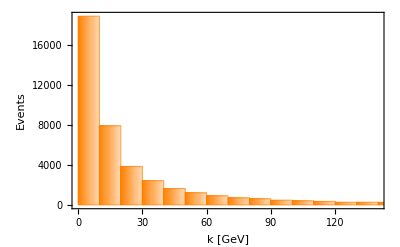

```mathematica
Histogram[KdistributionLB,{10},ChartElementFunction->"FadingRectangle",ChartStyle->Orange,Frame->True,FrameLabel->{"k [GeV]","Events"},LabelStyle->Directive[Black,Thickness[20],20,FontFamily->"Times"]]
```

```mathematica
Min[KdistributionLB]
```

0.127982

```mathematica
(*select events for k<mpi*)
```

```mathematica
Fselectevent[list_,limit_]:=Module[{ll,tt},ll=Length[list];tt={};Do[If[list[[i]]<limit,AppendTo[tt,list[[i]]]],{i,1,ll}];tt]
```

```mathematica
mpi=0.140;
```

```mathematica
t0=Fselectevent[KdistributionLB,mpi/2];
t1=Fselectevent[KdistributionLB,mpi];
t2=Fselectevent[KdistributionLB,2*mpi];
```

```mathematica
(*After the section, there is no event*)
```

```mathematica
t3=Fselectevent[KdistributionLB,2*mpi*10];
t4=Fselectevent[KdistributionLB,2*mpi*100];
```

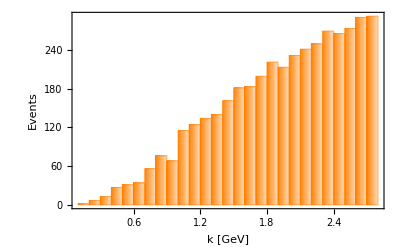

```mathematica
Histogram[t3,{0.1},ChartElementFunction->"FadingRectangle",ChartStyle->Orange,Frame->True,FrameLabel->{"k [GeV]","Events"},LabelStyle->Directive[Black,Thickness[20],20,FontFamily->"Times"]]
```

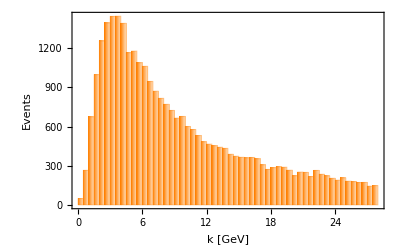

```mathematica
Histogram[t4,{0.5},ChartElementFunction->"FadingRectangle",ChartStyle->Orange,Frame->True,FrameLabel->{"k [GeV]","Events"},LabelStyle->Directive[Black,Thickness[20],20,FontFamily->"Times"]]
```

```mathematica
psi[r_]:=1/(Sqrt[2*Pi*a]*r)*Exp[-r/a]
```

```mathematica
Integrate[psi[r]^2*r^2*4*Pi,{r,0,Infinity}]
```

ConditionalExpression[1,Re[a]>0]

```mathematica
Integrate[psi[r]^2*r^4*4*Pi,{r,0,Infinity}]
```

ConditionalExpression[a^2/2,Re[a]>0]

#### Dstarbar Sigmac

```mathematica
data=Import["D_star_barSigma_c.dat"];
```

```mathematica
flab[px_,py_,pz_,kx_,ky_,kz_]:=Module[{p,k,t},p={px,py,pz};k={kx,ky,kz};t=Sum[(p[[i]]-k[[i]])^2,{i,1,3}];Sqrt[t]]
```

```mathematica
fLB[Ep_,px_,py_,pz_,Ek_,kx_,ky_,kz_]:=Module[{β,γ,q,Etot,qvec,kvec,costheta,k,kper,kpar,kparstar,Ekk,kstar},q=Sqrt[(px+kx)^2+(py+ky)^2+(pz+kz)^2];Etot=Ep+Ek;β=q/Etot;γ=1/Sqrt[1-β^2];qvec={px+kx,py+ky,pz+kz};kvec={px-kx,py-ky,pz-kz};
Ekk=Ep-Ek;
k=Sqrt[Sum[kvec[[i]]^2,{i,1,3}]];costheta=Sum[qvec[[i]]*kvec[[i]],{i,1,3}]/(k*q);kper=k*Sqrt[1-costheta^2];kpar=k*costheta;kparstar=-γ*β*Ekk+γ*kpar;kstar=Sqrt[kparstar^2+kper^2]]
```

```mathematica
KdistributionLB=Table[fLB[data[[i]][[14]],data[[i]][[11]],data[[i]][[12]],data[[i]][[13]],data[[i+2]][[14]],data[[i+2]][[11]],data[[i+2]][[12]],data[[i+2]][[13]]],{i,1,37715,4}];
```

```mathematica
kk=Table[{i,fLB[data[[i]][[14]],data[[i]][[11]],data[[i]][[12]],data[[i]][[13]],data[[i+2]][[14]],data[[i+2]][[11]],data[[i+2]][[12]],data[[i+2]][[13]]]},{i,1,37715,4}];
kb=Table[{i,flab[data[[i]][[11]],data[[i]][[12]],data[[i]][[13]],data[[i+2]][[11]],data[[i+2]][[12]],data[[i+2]][[13]]]},{i,1,37715,4}];
```

```mathematica
tcomp=Table[kk[[i,2]]-kb[[i,2]],{i,1,9379}];
```

```mathematica
(*Pan: Please check whether you obtin the same result. kk and kb are the lists of the relative momentum after and before Lorent Boost*)
```

```mathematica
Min[kk]
Min[kb]
```

0.108419

0.230803

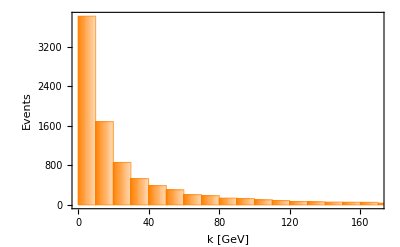

```mathematica
Histogram[KdistributionLB,{10},ChartElementFunction->"FadingRectangle",ChartStyle->Orange,Frame->True,FrameLabel->{"k [GeV]","Events"},LabelStyle->Directive[Black,Thickness[20],20,FontFamily->"Times"]]
```

```mathematica
Min[KdistributionLB]
```

0.108419

```mathematica
(*select events for k<mpi*)
```

```mathematica
Fselectevent[list_,limit_]:=Module[{ll,tt},ll=Length[list];tt={};Do[If[list[[i]]<limit,AppendTo[tt,list[[i]]]],{i,1,ll}];tt]
```

```mathematica
mpi=0.140;
```

```mathematica
t0=Fselectevent[KdistributionLB,mpi/2];
t1=Fselectevent[KdistributionLB,mpi];
t2=Fselectevent[KdistributionLB,2*mpi];
```

```mathematica
(*After the section, there is no event*)
```

```mathematica
t3=Fselectevent[KdistributionLB,2*mpi*10];
t4=Fselectevent[KdistributionLB,2*mpi*100];
```

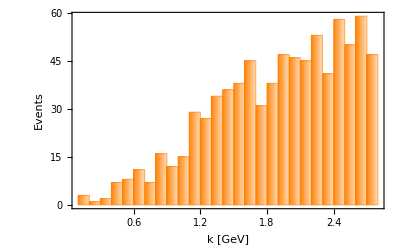

```mathematica
Histogram[t3,{0.1},ChartElementFunction->"FadingRectangle",ChartStyle->Orange,Frame->True,FrameLabel->{"k [GeV]","Events"},LabelStyle->Directive[Black,Thickness[20],20,FontFamily->"Times"]]
```

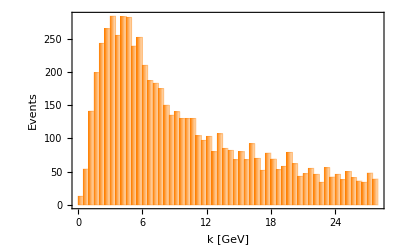

```mathematica
Histogram[t4,{0.5},ChartElementFunction->"FadingRectangle",ChartStyle->Orange,Frame->True,FrameLabel->{"k [GeV]","Events"},LabelStyle->Directive[Black,Thickness[20],20,FontFamily->"Times"]]
```

```mathematica
psi[r_]:=1/(Sqrt[2*Pi*a]*r)*Exp[-r/a]
```

```mathematica
Integrate[psi[r]^2*r^2*4*Pi,{r,0,Infinity}]
```

ConditionalExpression[1,Re[a]>0]

```mathematica
Integrate[psi[r]^2*r^4*4*Pi,{r,0,Infinity}]
```

ConditionalExpression[a^2/2,Re[a]>0]

#### Dstarbar Sigmastarc

```mathematica
data=Import["D_star_barSigma_star_c.dat"];
```

```mathematica
flab[px_,py_,pz_,kx_,ky_,kz_]:=Module[{p,k,t},p={px,py,pz};k={kx,ky,kz};t=Sum[(p[[i]]-k[[i]])^2,{i,1,3}];Sqrt[t]]
```

```mathematica
fLB[Ep_,px_,py_,pz_,Ek_,kx_,ky_,kz_]:=Module[{β,γ,q,Etot,qvec,kvec,costheta,k,kper,kpar,kparstar,Ekk,kstar},q=Sqrt[(px+kx)^2+(py+ky)^2+(pz+kz)^2];Etot=Ep+Ek;β=q/Etot;γ=1/Sqrt[1-β^2];qvec={px+kx,py+ky,pz+kz};kvec={px-kx,py-ky,pz-kz};
Ekk=Ep-Ek;
k=Sqrt[Sum[kvec[[i]]^2,{i,1,3}]];costheta=Sum[qvec[[i]]*kvec[[i]],{i,1,3}]/(k*q);kper=k*Sqrt[1-costheta^2];kpar=k*costheta;kparstar=-γ*β*Ekk+γ*kpar;kstar=Sqrt[kparstar^2+kper^2]]
```

```mathematica
KdistributionLB=Table[fLB[data[[i]][[14]],data[[i]][[11]],data[[i]][[12]],data[[i]][[13]],data[[i+2]][[14]],data[[i+2]][[11]],data[[i+2]][[12]],data[[i+2]][[13]]],{i,1,60291,4}];
```

```mathematica
kk=Table[{i,fLB[data[[i]][[14]],data[[i]][[11]],data[[i]][[12]],data[[i]][[13]],data[[i+2]][[14]],data[[i+2]][[11]],data[[i+2]][[12]],data[[i+2]][[13]]]},{i,1,60291,4}];
kb=Table[{i,flab[data[[i]][[11]],data[[i]][[12]],data[[i]][[13]],data[[i+2]][[11]],data[[i+2]][[12]],data[[i+2]][[13]]]},{i,1,60291,4}];
```

```mathematica
tcomp=Table[kk[[i,2]]-kb[[i,2]],{i,1,15023}];
```

```mathematica
(*Pan: Please check whether you obtin the same result. kk and kb are the lists of the relative momentum after and before Lorent Boost*)
```

```mathematica
Min[kk]
Min[kb]
```

0.158171

0.218252

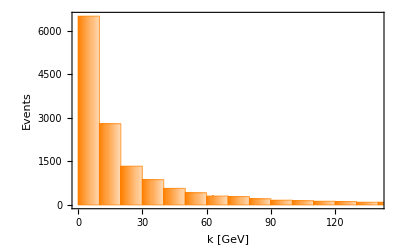

```mathematica
Histogram[KdistributionLB,{10},ChartElementFunction->"FadingRectangle",ChartStyle->Orange,Frame->True,FrameLabel->{"k [GeV]","Events"},LabelStyle->Directive[Black,Thickness[20],20,FontFamily->"Times"]]
```

```mathematica
Min[KdistributionLB]
```

0.158171

```mathematica
(*select events for k<mpi*)
```

```mathematica
Fselectevent[list_,limit_]:=Module[{ll,tt},ll=Length[list];tt={};Do[If[list[[i]]<limit,AppendTo[tt,list[[i]]]],{i,1,ll}];tt]
```

```mathematica
mpi=0.140;
```

```mathematica
t0=Fselectevent[KdistributionLB,mpi/2];
t1=Fselectevent[KdistributionLB,mpi];
t2=Fselectevent[KdistributionLB,2*mpi];
```

```mathematica
(*After the section, there is no event*)
```

```mathematica
t3=Fselectevent[KdistributionLB,2*mpi*10];
t4=Fselectevent[KdistributionLB,2*mpi*100];
```

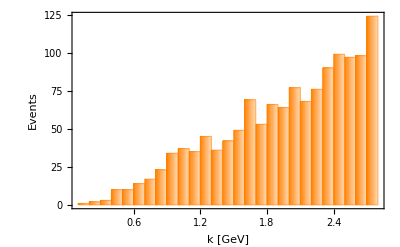

```mathematica
Histogram[t3,{0.1},ChartElementFunction->"FadingRectangle",ChartStyle->Orange,Frame->True,FrameLabel->{"k [GeV]","Events"},LabelStyle->Directive[Black,Thickness[20],20,FontFamily->"Times"]]
```

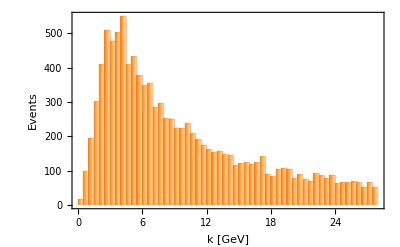

```mathematica
Histogram[t4,{0.5},ChartElementFunction->"FadingRectangle",ChartStyle->Orange,Frame->True,FrameLabel->{"k [GeV]","Events"},LabelStyle->Directive[Black,Thickness[20],20,FontFamily->"Times"]]
```

```mathematica
psi[r_]:=1/(Sqrt[2*Pi*a]*r)*Exp[-r/a]
```

```mathematica
Integrate[psi[r]^2*r^2*4*Pi,{r,0,Infinity}]
```

ConditionalExpression[1,Re[a]>0]

```mathematica
Integrate[psi[r]^2*r^4*4*Pi,{r,0,Infinity}]
```

ConditionalExpression[a^2/2,Re[a]>0]